Copyright ©, 2015, Erdong Guo and Shu Lin
Author: Erdong Guo and Shu Lin
E-mail: guoerdong@itp.ac.cn, linshu8@mail.sysu.edu.cn
Affliation: Institute of Theoretical Physics, Chinese Academy of Scineces, School of Physics and Astronomy, Sun-Yat Sen University
Description: Calculation tools for AdS/QCD. Free energy, quark mass, quark condensation, and other quantities in QFT side are calculated by D3/D7 model.

```mathematica
Quit[]
```

```mathematica
H=1+1/#^4&;f=1-1/#^4&;
gtt=-r0^2/2 #^2 f[#]^2/H[#]&;
gxx=r0^2/2 #^2 H[#]&;
gphiphi=chi[#]^2&;
grhorho=1/#^2&;
```

```mathematica
L=Simplify[Sqrt[-gtt[rho] gxx[rho](gxx[rho]^2+B^2)(grhorho[rho]+chi'[rho]^2/(1-chi[rho]^2))(1-chi[rho]^2)^3]/.{r0-> 1},Assumptions->rho>1&&chi[rho]<1&&chi[rho]>0];
```

```mathematica
eom=3 (-1+rho^4) (1+(2+4 B^2) rho^4+rho^8) chi[rho]^3-(-1+rho^4) (1+(2+4 B^2) rho^4+rho^8) chi[rho] (3+4 rho^2 chi'[rho]^2)+rho (-(3+rho^4 (3+4 B^2 (1+3 rho^4)+5 (rho^4+rho^8))) chi'[rho]-4 rho^2 (1+rho^4) (1+2 B^2 rho^4+rho^8) chi'[rho]^3-rho (-1+rho^4) (1+(2+4 B^2) rho^4+rho^8) chi''[rho])+rho chi[rho]^2 ((3+rho^4 (3+4 B^2 (1+3 rho^4)+5 (rho^4+rho^8))) chi'[rho]+rho (-1+rho^4) (1+(2+4 B^2) rho^4+rho^8) chi''[rho]);
```

module for calculating the mass, condensation and free energy in black hole imbedding

```mathematica
FreeEnergyB[Chi0_,nB_,eps_,uv_]:=
Module[{sol,data,rep},
sol=NDSolve[{eom==0,chi[1+eps]==Chi0+eps^2/2 chi2+eps^3/6 chi3,chi'[1+eps]==eps chi2+eps^2/2 chi3}/.{chi2-> -3/2 Chi0,chi3-> 9/2 Chi0,B-> nB},chi,{rho,1+eps,uv},AccuracyGoal->20,PrecisionGoal->20,WorkingPrecision->25];data=Table[{rho,rho chi[rho]/.sol[[1]]}/.{rho->uv-i},{i,5}];{rep=FindFit[data,m+c/rho^2,{m,c},rho],FE=NIntegrate[L/.sol[[1]]/.rep/.{B->nB},{rho,1+eps,uv},AccuracyGoal->16,PrecisionGoal->16,WorkingPrecision->25]-(1/16(((uv^2-m^2)^2-4 m c)/.rep)+B^2/2 Log[uv]/.{B->nB})}]
```

output format is “mass, quark condensation and free energy”.

```mathematica
FreeEnergyB[1/5,2,1/100,100]
```

{{m→0.247682359551413544210162,c→0.388190055891611205571039},-1.13248493221987012}

```mathematica
FreeEnergyB[1-1/100,0,1/10000,200]
```

{{m→1.30198,c→0.365275},-0.0100261}

```mathematica
chimi=chi0;
```

```mathematica
pchimi=-((2 a^2 (-1+a^4) (1+a^8+a^4 (2+4 B^2)) chi0+(a^4 (-9+13 chi0^2+a^24 (-15+19 chi0^2)-16 a^12 (3-2 chi0^2-2 B^2 (-3+chi0^2)+2 B^4 (3+chi0^2))+a^8 (-33+29 chi0^2+84 B^2 (-1+chi0^2)+8 B^4 (-3+11 chi0^2))+a^16 (-39+35 chi0^2+108 B^2 (-1+chi0^2)+8 B^4 (-9+17 chi0^2))+2 a^4 (-9+13 chi0^2+B^2 (-15+31 chi0^2))+a^20 (-30+38 chi0^2+B^2 (-66+98 chi0^2))))/(-54 a^6 chi0-162 a^10 chi0-198 a^14 chi0-162 a^18 chi0-54 a^22 chi0+126 a^26 chi0+198 a^30 chi0+162 a^34 chi0+108 a^38 chi0+36 a^42 chi0-450 a^10 B^2 chi0-846 a^14 B^2 chi0-666 a^18 B^2 chi0-198 a^22 B^2 chi0+522 a^26 B^2 chi0+774 a^30 B^2 chi0+594 a^34 B^2 chi0+270 a^38 B^2 chi0-1188 a^14 B^4 chi0-1260 a^18 B^4 chi0-72 a^22 B^4 chi0+648 a^26 B^4 chi0+1260 a^30 B^4 chi0+612 a^34 B^4 chi0-1008 a^18 B^6 chi0-432 a^22 B^6 chi0+1008 a^26 B^6 chi0+432 a^30 B^6 chi0+46 a^6 chi0^3+138 a^10 chi0^3+198 a^14 chi0^3+226 a^18 chi0^3+102 a^22 chi0^3-174 a^26 chi0^3-262 a^30 chi0^3-162 a^34 chi0^3-84 a^38 chi0^3-28 a^42 chi0^3+354 a^10 B^2 chi0^3+750 a^14 B^2 chi0^3+954 a^18 B^2 chi0^3+486 a^22 B^2 chi0^3-810 a^26 B^2 chi0^3-1062 a^30 B^2 chi0^3-498 a^34 B^2 chi0^3-174 a^38 B^2 chi0^3+804 a^14 B^4 chi0^3+1644 a^18 B^4 chi0^3+840 a^22 B^4 chi0^3-1416 a^26 B^4 chi0^3-1644 a^30 B^4 chi0^3-228 a^34 B^4 chi0^3+496 a^18 B^6 chi0^3+1968 a^22 B^6 chi0^3-2544 a^26 B^6 chi0^3+80 a^30 B^6 chi0^3+√(a^12 ((-4 (-1+a^4)^2 (1+a^8+a^4 (2+4 B^2))^2 chi0^2-3 (1+a^4) (1+a^8+2 a^4 B^2) (3+5 a^12+a^4 (3+4 B^2)+a^8 (5+12 B^2)) (-1+chi0^2))^3+4 (-1+a^4)^2 (1+a^8+a^4 (2+4 B^2))^2 chi0^2 (-27+23 chi0^2+2 a^24 (-9+7 chi0^2)-a^16 (63-67 chi0^2-162 B^2 (-1+chi0^2)+2 B^4 (27+5 chi0^2))+a^20 (4 (-9+7 chi0^2)+B^2 (-63+31 chi0^2))+2 a^8 (-36+38 chi0^2+99 B^2 (-1+chi0^2)+B^4 (-63+31 chi0^2))+2 a^12 (-45+53 chi0^2+2 B^2 (-45+61 chi0^2)+2 B^4 (-45+77 chi0^2))+a^4 (-54+46 chi0^2+B^2 (-117+85 chi0^2)))^2)))^(1/3)+(-54 a^6 chi0-162 a^10 chi0-198 a^14 chi0-162 a^18 chi0-54 a^22 chi0+126 a^26 chi0+198 a^30 chi0+162 a^34 chi0+108 a^38 chi0+36 a^42 chi0-450 a^10 B^2 chi0-846 a^14 B^2 chi0-666 a^18 B^2 chi0-198 a^22 B^2 chi0+522 a^26 B^2 chi0+774 a^30 B^2 chi0+594 a^34 B^2 chi0+270 a^38 B^2 chi0-1188 a^14 B^4 chi0-1260 a^18 B^4 chi0-72 a^22 B^4 chi0+648 a^26 B^4 chi0+1260 a^30 B^4 chi0+612 a^34 B^4 chi0-1008 a^18 B^6 chi0-432 a^22 B^6 chi0+1008 a^26 B^6 chi0+432 a^30 B^6 chi0+46 a^6 chi0^3+138 a^10 chi0^3+198 a^14 chi0^3+226 a^18 chi0^3+102 a^22 chi0^3-174 a^26 chi0^3-262 a^30 chi0^3-162 a^34 chi0^3-84 a^38 chi0^3-28 a^42 chi0^3+354 a^10 B^2 chi0^3+750 a^14 B^2 chi0^3+954 a^18 B^2 chi0^3+486 a^22 B^2 chi0^3-810 a^26 B^2 chi0^3-1062 a^30 B^2 chi0^3-498 a^34 B^2 chi0^3-174 a^38 B^2 chi0^3+804 a^14 B^4 chi0^3+1644 a^18 B^4 chi0^3+840 a^22 B^4 chi0^3-1416 a^26 B^4 chi0^3-1644 a^30 B^4 chi0^3-228 a^34 B^4 chi0^3+496 a^18 B^6 chi0^3+1968 a^22 B^6 chi0^3-2544 a^26 B^6 chi0^3+80 a^30 B^6 chi0^3+√(a^12 ((-4 (-1+a^4)^2 (1+a^8+a^4 (2+4 B^2))^2 chi0^2-3 (1+a^4) (1+a^8+2 a^4 B^2) (3+5 a^12+a^4 (3+4 B^2)+a^8 (5+12 B^2)) (-1+chi0^2))^3+4 (-1+a^4)^2 (1+a^8+a^4 (2+4 B^2))^2 chi0^2 (-27+23 chi0^2+2 a^24 (-9+7 chi0^2)-a^16 (63-67 chi0^2-162 B^2 (-1+chi0^2)+2 B^4 (27+5 chi0^2))+a^20 (4 (-9+7 chi0^2)+B^2 (-63+31 chi0^2))+2 a^8 (-36+38 chi0^2+99 B^2 (-1+chi0^2)+B^4 (-63+31 chi0^2))+2 a^12 (-45+53 chi0^2+2 B^2 (-45+61 chi0^2)+2 B^4 (-45+77 chi0^2))+a^4 (-54+46 chi0^2+B^2 (-117+85 chi0^2)))^2)))^(1/3))/(6 a^3 (1+a^4) (1+a^8+2 a^4 B^2)));
```

module for calculating the mass, condensation and free energy in Minkowski imbedding

```mathematica
FreeEnergyM[a0_,nB_,eps_,uv_]:=
Module[{sol,data,rep},
sol=NDSolve[{eom==0,chi[a0]==chi0,chi'[a0]==pchimi}/.{a->a0,chi0-> 1-eps,B-> nB},chi,{rho,a0,uv},AccuracyGoal->20,PrecisionGoal->20,WorkingPrecision->25];data=Table[{rho,rho chi[rho]/.sol[[1]]}/.{rho->uv-i},{i,5}];{rep=FindFit[data,m+c/rho^2,{m,c},rho],FE=NIntegrate[L/.sol[[1]]/.rep/.{B->nB},{rho,a0,uv},AccuracyGoal->16,PrecisionGoal->16,WorkingPrecision->25]-(1/16(((uv^2-m^2)^2-4 m c)/.rep)+B^2/2 Log[uv]/.{B->nB})}]
```

```mathematica
FreeEnergyM[3/2,2,1/1000,100]
```

{{m→1.03306742081954786969668,c→1.96584626404111264372086},-1.59058329093931945}

```mathematica
FreeEnergyM[1000001/1000000,33/5,1/1000,200]
```

{{m→-0.00906941052488555859097605,c→8.64332667446377004728493},-17.8750558389652929}

```mathematica
FreeEnergyM[1000001/1000000,0,1/1000,200]
```

{{m→1.29676112895149396143422,c→-0.064183433036144420721163},-0.0079430208686095}

test the IR stability of the numerical result

```mathematica
FreeEnergyM[1000100/1000000,2,1/10,200]
```

{{m→0.866954199060504429396209,c→1.76354405568286000922519},-1.4281943791297658}

```mathematica
FreeEnergyM[1000100/1000000,2,1/100,200]
```

{{m→0.833260034650896679685668,c→1.8428634694188534994821},-1.3973762599470102}

```mathematica
FreeEnergyM[1000100/1000000,2,1/1000,200]
```

{{m→0.828381066336896488396826,c→1.83884936720996899743393},-1.3928839237142211}

```mathematica
FreeEnergyM[1000100/1000000,2,1/10000,200]
```

{{m→0.828444187529024840742815,c→1.83856035890212466969985},-1.3929419398554498}

test the UV stability of the numerical result

```mathematica
FreeEnergyM[1000100/1000000,2,1/10000,100]
```

{{m→0.828444209391776364104028,c→1.83822931316681098148472},-1.39296574658040456}

```mathematica
FreeEnergyM[1000100/1000000,2,1/10000,50]
```

{{m→0.828444610424501220263382,c→1.83679606559113294013753},-1.393058272905497733}

```mathematica
FreeEnergyM[1000100/1000000,2,1/10000,300]
```

{{m→0.828444186429765804388693,c→1.83861960994153633322098},-1.392937504584386}

```mathematica
FreeEnergyM[1000100/1000000,2,1/10000,400]
```

{{m→0.828458,c→0.274437},-1.39354}

```mathematica
FreeEnergyM[1000100/1000000,2,1/10000,500]
```

{{m→0.828456,c→-0.709364},-1.39336}

plotting the critical m-B diagram using the Minkowski imbedding

```mathematica
datam=Table[{Pi^2 i/20,2 FreeEnergyM[1.000001,i/20,1/1000,200][[1]][[1]][[-1]]},{i,131}]
```

{{π^2/20,2.5924},{π^2/10,2.58911},{(3 π^2)/20,2.58366},{π^2/5,2.57609},{π^2/4,2.56647},{(3 π^2)/10,2.55486},{(7 π^2)/20,2.54138},{(2 π^2)/5,2.5261},{(9 π^2)/20,2.50914},{π^2/2,2.49061},{(11 π^2)/20,2.47063},{(3 π^2)/5,2.44932},{(13 π^2)/20,2.42677},{(7 π^2)/10,2.40314},{(3 π^2)/4,2.3785},{(4 π^2)/5,2.35297},{(17 π^2)/20,2.32665},{(9 π^2)/10,2.29964},{(19 π^2)/20,2.27204},{π^2,2.2439},{(21 π^2)/20,2.21533},{(11 π^2)/10,2.1864},{(23 π^2)/20,2.15716},{(6 π^2)/5,2.12769},{(5 π^2)/4,2.09804},{(13 π^2)/10,2.06824},{(27 π^2)/20,2.03837},{(7 π^2)/5,2.00846},{(29 π^2)/20,1.97854},{(3 π^2)/2,1.94865},{(31 π^2)/20,1.91882},{(8 π^2)/5,1.88908},{(33 π^2)/20,1.85945},{(17 π^2)/10,1.82996},{(7 π^2)/4,1.80061},{(9 π^2)/5,1.77144},{(37 π^2)/20,1.74245},{(19 π^2)/10,1.71367},{(39 π^2)/20,1.68511},{2 π^2,1.65676},{(41 π^2)/20,1.62865},{(21 π^2)/10,1.60077},{(43 π^2)/20,1.57314},{(11 π^2)/5,1.54575},{(9 π^2)/4,1.51863},{(23 π^2)/10,1.49176},{(47 π^2)/20,1.46516},{(12 π^2)/5,1.43882},{(49 π^2)/20,1.41274},{(5 π^2)/2,1.38693},{(51 π^2)/20,1.3614},{(13 π^2)/5,1.33612},{(53 π^2)/20,1.31111},{(27 π^2)/10,1.28637},{(11 π^2)/4,1.26189},{(14 π^2)/5,1.23768},{(57 π^2)/20,1.21373},{(29 π^2)/10,1.19004},{(59 π^2)/20,1.16661},{3 π^2,1.14344},{(61 π^2)/20,1.12052},{(31 π^2)/10,1.09786},{(63 π^2)/20,1.07544},{(16 π^2)/5,1.05328},{(13 π^2)/4,1.03134},{(33 π^2)/10,1.00966},{(67 π^2)/20,0.988215},{(17 π^2)/5,0.967009},{(69 π^2)/20,0.946036},{(7 π^2)/2,0.925295},{(71 π^2)/20,0.904791},{(18 π^2)/5,0.884503},{(73 π^2)/20,0.86443},{(37 π^2)/10,0.844583},{(15 π^2)/4,0.824952},{(19 π^2)/5,0.805533},{(77 π^2)/20,0.786326},{(39 π^2)/10,0.767325},{(79 π^2)/20,0.748539},{4 π^2,0.729946},{(81 π^2)/20,0.711547},{(41 π^2)/10,0.69335},{(83 π^2)/20,0.675345},{(21 π^2)/5,0.657532},{(17 π^2)/4,0.639907},{(43 π^2)/10,0.622468},{(87 π^2)/20,0.60522},{(22 π^2)/5,0.588144},{(89 π^2)/20,0.571246},{(9 π^2)/2,0.554523},{(91 π^2)/20,0.537967},{(23 π^2)/5,0.521587},{(93 π^2)/20,0.505381},{(47 π^2)/10,0.489335},{(19 π^2)/4,0.473445},{(24 π^2)/5,0.457725},{(97 π^2)/20,0.442162},{(49 π^2)/10,0.426753},{(99 π^2)/20,0.411498},{5 π^2,0.396395},{(101 π^2)/20,0.381442},{(51 π^2)/10,0.366636},{(103 π^2)/20,0.351975},{(26 π^2)/5,0.337457},{(21 π^2)/4,0.323083},{(53 π^2)/10,0.308847},{(107 π^2)/20,0.294748},{(27 π^2)/5,0.280784},{(109 π^2)/20,0.266955},{(11 π^2)/2,0.253256},{(111 π^2)/20,0.239688},{(28 π^2)/5,0.226248},{(113 π^2)/20,0.212934},{(57 π^2)/10,0.199745},{(23 π^2)/4,0.186679},{(29 π^2)/5,0.173734},{(117 π^2)/20,0.16091},{(59 π^2)/10,0.148203},{(119 π^2)/20,0.135612},{6 π^2,0.123137},{(121 π^2)/20,0.110787},{(61 π^2)/10,0.0985354},{(123 π^2)/20,0.0863911},{(31 π^2)/5,0.0743509},{(25 π^2)/4,0.0624295},{(63 π^2)/10,0.0506042},{(127 π^2)/20,0.0388938},{(32 π^2)/5,0.0272844},{(129 π^2)/20,0.015776},{(13 π^2)/2,0.00436641},{(131 π^2)/20,-0.00691354}}

```mathematica
ListLinePlot[datam,PlotRange->All,AxesLabel->{B,m}]
```

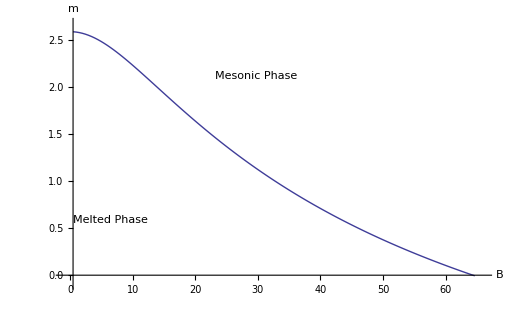

plotting the critical m-B diagram using the black hole imbedding

```mathematica
datab=Table[{Pi^2 i/20,2 FreeEnergyB[1-1/1000,i/20,1/1000,200][[1]][[1]][[-1]]},{i,131}]
```

{{π^2/20,2.59241},{π^2/10,2.58911},{(3 π^2)/20,2.58366},{π^2/5,2.57609},{π^2/4,2.56647},{(3 π^2)/10,2.55485},{(7 π^2)/20,2.54138},{(2 π^2)/5,2.5261},{(9 π^2)/20,2.50914},{π^2/2,2.49061},{(11 π^2)/20,2.47063},{(3 π^2)/5,2.44932},{(13 π^2)/20,2.42678},{(7 π^2)/10,2.40314},{(3 π^2)/4,2.3785},{(4 π^2)/5,2.35297},{(17 π^2)/20,2.32665},{(9 π^2)/10,2.29964},{(19 π^2)/20,2.27203},{π^2,2.2439},{(21 π^2)/20,2.21533},{(11 π^2)/10,2.1864},{(23 π^2)/20,2.15716},{(6 π^2)/5,2.1277},{(5 π^2)/4,2.09804},{(13 π^2)/10,2.06824},{(27 π^2)/20,2.03837},{(7 π^2)/5,2.00846},{(29 π^2)/20,1.97855},{(3 π^2)/2,1.94866},{(31 π^2)/20,1.91882},{(8 π^2)/5,1.88907},{(33 π^2)/20,1.85945},{(17 π^2)/10,1.82995},{(7 π^2)/4,1.80061},{(9 π^2)/5,1.77144},{(37 π^2)/20,1.74246},{(19 π^2)/10,1.71368},{(39 π^2)/20,1.68511},{2 π^2,1.65676},{(41 π^2)/20,1.62864},{(21 π^2)/10,1.60076},{(43 π^2)/20,1.57313},{(11 π^2)/5,1.54575},{(9 π^2)/4,1.51863},{(23 π^2)/10,1.49176},{(47 π^2)/20,1.46516},{(12 π^2)/5,1.43882},{(49 π^2)/20,1.41273},{(5 π^2)/2,1.38694},{(51 π^2)/20,1.3614},{(13 π^2)/5,1.33611},{(53 π^2)/20,1.31112},{(27 π^2)/10,1.28636},{(11 π^2)/4,1.26189},{(14 π^2)/5,1.23768},{(57 π^2)/20,1.21373},{(29 π^2)/10,1.19004},{(59 π^2)/20,1.16661},{3 π^2,1.14343},{(61 π^2)/20,1.12052},{(31 π^2)/10,1.09786},{(63 π^2)/20,1.07543},{(16 π^2)/5,1.05326},{(13 π^2)/4,1.03134},{(33 π^2)/10,1.00966},{(67 π^2)/20,0.988215},{(17 π^2)/5,0.967009},{(69 π^2)/20,0.946036},{(7 π^2)/2,0.925294},{(71 π^2)/20,0.904791},{(18 π^2)/5,0.884502},{(73 π^2)/20,0.86443},{(37 π^2)/10,0.844582},{(15 π^2)/4,0.824951},{(19 π^2)/5,0.805533},{(77 π^2)/20,0.786327},{(39 π^2)/10,0.767328},{(79 π^2)/20,0.748533},{4 π^2,0.72994},{(81 π^2)/20,0.711548},{(41 π^2)/10,0.693352},{(83 π^2)/20,0.675348},{(21 π^2)/5,0.657535},{(17 π^2)/4,0.639908},{(43 π^2)/10,0.62247},{(87 π^2)/20,0.605215},{(22 π^2)/5,0.588146},{(89 π^2)/20,0.571241},{(9 π^2)/2,0.554522},{(91 π^2)/20,0.537974},{(23 π^2)/5,0.521591},{(93 π^2)/20,0.505377},{(47 π^2)/10,0.489334},{(19 π^2)/4,0.47345},{(24 π^2)/5,0.457729},{(97 π^2)/20,0.442164},{(49 π^2)/10,0.426753},{(99 π^2)/20,0.411497},{5 π^2,0.396397},{(101 π^2)/20,0.381444},{(51 π^2)/10,0.366637},{(103 π^2)/20,0.351976},{(26 π^2)/5,0.33746},{(21 π^2)/4,0.323083},{(53 π^2)/10,0.308849},{(107 π^2)/20,0.29475},{(27 π^2)/5,0.280787},{(109 π^2)/20,0.266957},{(11 π^2)/2,0.253259},{(111 π^2)/20,0.23969},{(28 π^2)/5,0.22625},{(113 π^2)/20,0.212936},{(57 π^2)/10,0.199747},{(23 π^2)/4,0.186681},{(29 π^2)/5,0.173734},{(117 π^2)/20,0.160909},{(59 π^2)/10,0.148205},{(119 π^2)/20,0.135613},{6 π^2,0.12315},{(121 π^2)/20,0.110783},{(61 π^2)/10,0.0985204},{(123 π^2)/20,0.0863768},{(31 π^2)/5,0.0743544},{(25 π^2)/4,0.0624319},{(63 π^2)/10,0.0506096},{(127 π^2)/20,0.0388943},{(32 π^2)/5,0.0272852},{(129 π^2)/20,0.0157751},{(13 π^2)/2,0.00436604},{(131 π^2)/20,-0.00692161}}

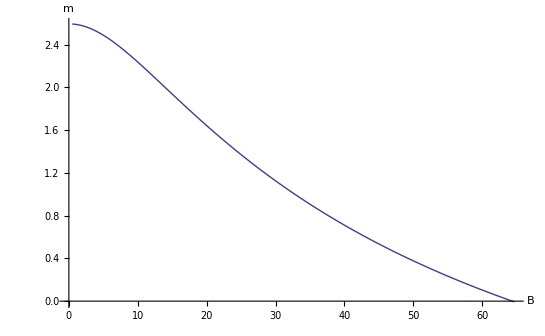

```mathematica
ListLinePlot[datab,AxesLabel->{B,m}]
```

```mathematica
datam=Table[{1/(FreeEnergyM[1+i/10,0,1/100,100][[-2]][[1]][[-1]]),FreeEnergyM[1+i/10,0,1/100,100][[-1]]},{i,20}]
```

{{0.772052283895434549667126,-0.008012668065195846},{0.760876119565420966868803,-0.007481186904657134},{0.733355137940991446025086,-0.006353852316236318},{0.697793095317332359069179,-0.00516441726516709},{0.660239639798233509662581,-0.00414699056004254},{0.623799292239572142370996,-0.00334700085142389},{0.589757322639246894704156,-0.00274171843213794},{0.55848886164671931984172,-0.00229391683036561},{0.529961055047306020598291,-0.00196958304240401},{0.50397782849037054300574,-0.00174191769340772},{0.480292325579238944682939,-0.00159098006046121},{0.458656041398333991369946,-0.00150232025605666},{0.438838582576859892945702,-0.00146562088967046},{0.420634091180946121374645,-0.00147361194557003},{0.403861813072073873685368,-0.0015212573037428},{0.388364276718268179903223,-0.00160516460963994},{0.374004669248334503189345,-0.00172316672166635},{0.360664115129747565262608,-0.00187401187342362},{0.348239149781244734397968,-0.00205714887280096},{0.336639488818077578717473,-0.00227256697218064}}

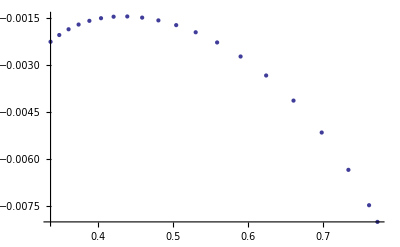

```mathematica
ListPlot[datam]
```

```mathematica
datab=Table[{1/(FreeEnergyB[i/10,0,1/100,100][[-2]][[1]][[-1]]),FreeEnergyB[i/10,0,1/100,100][[-1]]},{i,9}]
```

{{5.99771576078668648485871,-0.12194170940154162},{3.00957398622584578009667,-0.11279135397259418},{2.01874500770137551385205,-0.098589544711215981},{1.52782773302569800120306,-0.080827321719301516},{1.23766883184573182563481,-0.06142365669032533},{1.04901144751697102221627,-0.04254605045674616},{0.920079939136239947003417,-0.02636103445926418},{0.831514925526099717282516,-0.01469393632511459},{0.776651659157356425327577,-0.008574261090332727}}

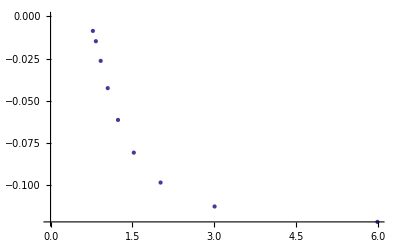

```mathematica
ListPlot[datab]
```

```mathematica
datam=Table[{1/(FreeEnergyM[1+i/100,0,1/100,100][[-2]][[1]][[-1]]),FreeEnergyM[1+i/100,0,1/100,100][[-1]]},{i,20}]
```

{{0.768113960285802486116334,-0.00778281826638285},{0.768411770479741725298851,-0.007799742425836769},{0.768944510558133029097674,-0.007829937567720513},{0.769622429303290736664558,-0.0078685029089671},{0.770328332572485127183318,-0.00790892126410583},{0.770970977076415115420309,-0.007946025239404475},{0.771493550990357868898255,-0.007976556766957302},{0.771861471468852525848322,-0.007998553193354311},{0.772052598479517909240714,-0.008010822461167469},{0.772052283895434549667126,-0.008012668065195846},{0.771851003327963349068317,-0.008003748953978194},{0.771443106307854025250004,-0.007983997321157826},{0.770826045976215300454498,-0.007953560611421821},{0.769999830229349688896566,-0.007912757307917816},{0.768966588612911462212414,-0.007862039421478169},{0.767730209468864422116423,-0.007801960178159348},{0.766296026348378283500806,-0.007733146392824615},{0.764670543120895586818396,-0.007656273841288338},{0.762861191839762655111018,-0.007572047827104666},{0.760876119565420966868803,-0.007481186904657134}}

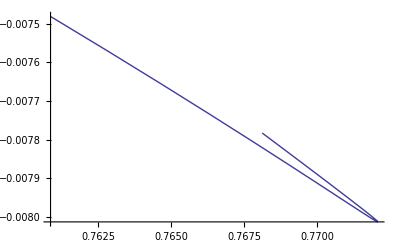

```mathematica
ListLinePlot[datam]
```

```mathematica
datab=Table[{1/(FreeEnergyB[9/10+i/100,0,1/100,100][[-2]][[1]][[-1]]),FreeEnergyB[9/10+i/100,0,1/100,100][[-1]]},{i,9}]
```

{{0.773202506342309155496001,-0.008270993509725492},{0.770208355546901270915868,-0.008021379616796736},{0.767712089753388662826052,-0.007824653198688933},{0.765769548159151717587856,-0.007680235364735086},{0.76445445286625513095386,-0.007587957534107938},{0.763865827716539333576678,-0.007548440424352317},{0.764139043392964091590047,-0.007563733978508504},{0.765459631613765684630377,-0.007638315245619897},{0.768051099849292552584667,-0.007779422772985317}}

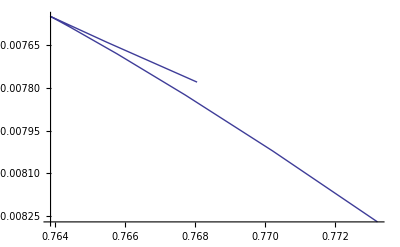

```mathematica
ListLinePlot[datab]
```

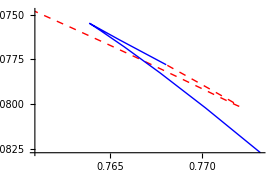

```mathematica
ListLinePlot[{datam,datab},PlotStyle->{{Red,Dashed},Blue}]
```

```mathematica
F[0]={0.7668,-0.007759};
```

```mathematica
datam=Table[{1/(FreeEnergyM[1+i/1000,1,1/100,100][[-2]][[1]][[-1]]),FreeEnergyM[1+i/1000,1,1/100,100][[-1]]},{i,20}]
```

{{0.886922227270824222892124,-0.38597517094773582},{0.886919741770324257475932,-0.385975980728638},{0.886917590884062095320922,-0.3859766909869523},{0.886916433098655559332722,-0.38597709025510826},{0.886916718743514818870174,-0.38597703384701766},{0.8869187854306985213011,-0.38597641337677802},{0.886922898681918889534333,-0.38597514361342119},{0.8869292732231625041835,-0.38597315562312407},{0.886938085566094618260559,-0.38597039277263013},{0.886949482037988193382888,-0.38596680808287137},{0.886963584180360486556486,-0.38596236270910072},{0.886980492508320732219516,-0.38595702434472222},{0.887000289189905834968337,-0.38595076703580512},{0.887023039982973962164438,-0.38594356952292584},{0.887048795647072682561126,-0.38593541588540386},{0.887077592977662361794645,-0.38592629448326734},{0.887109455568356437900445,-0.38591619798680511},{0.887144394380761632258268,-0.38590512317469445},{0.887182408183872451516371,-0.38589307073583404},{0.887223483913468295926738,-0.3858800451091782}}

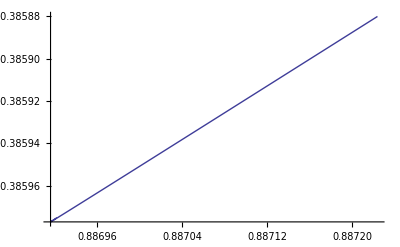

```mathematica
ListLinePlot[datam]
```

```mathematica
datab=Table[{1/(FreeEnergyB[9/10+9/100+5/1000+i/2000,1,1/100,100][[-2]][[1]][[-1]]),FreeEnergyB[9/10+9/100+5/1000+i/2000,1,1/100,100][[-1]]},{i,9}]
```

{{0.889882041693865301947671,-0.38502810160193237},{0.890133448047129692093147,-0.38494794771683746},{0.890375796031861201883349,-0.38487073736487165},{0.890606230582955994591562,-0.38479737534673685},{0.890820947506202581693749,-0.3847290657380953},{0.891014694897679015138169,-0.38466746986078557},{0.89117986270027967539766,-0.38461499390279721},{0.891304630746411577482917,-0.38457537571767421},{0.891368611758968533373006,-0.38455506617019863}}

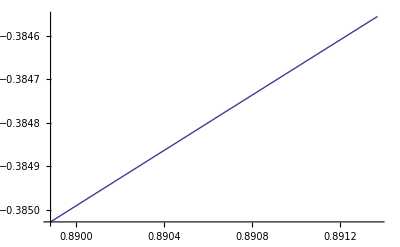

```mathematica
ListLinePlot[datab]
```

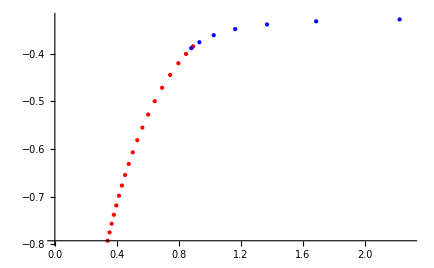

```mathematica
ListPlot[{datam,datab},PlotStyle->{Red,Blue}]
```

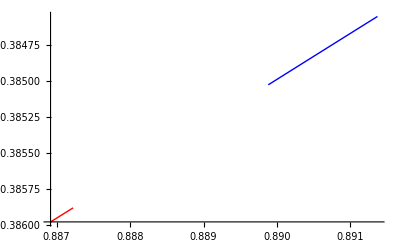

```mathematica
ListLinePlot[{datam,datab},PlotStyle->{Red,Blue}]
```

```mathematica
datab=Table[
```

```mathematica
F[1]={0.8886,-0.3854};
```

```mathematica
datam=Table[{1/(FreeEnergyM[1+i/10,2,1/100,100][[-2]][[1]][[-1]]),FreeEnergyM[1+i/10,2,1/100,100][[-1]]},{i,20}]
```

{{1.20940926656540751784631,-1.39154121645070639},{1.20122814410395108392082,-1.39681529442306332},{1.15182493810017722901427,-1.43051535690438454},{1.071657277220639194262,-1.49303957437422813},{0.978776539693832706330971,-1.57961336521327756},{0.886930664726938570043934,-1.68377649165078669},{0.803300253689161363056197,-1.79906781046391734},{0.73031430964608162382835,-1.91993383041648965},{0.667864816085807854309942,-2.04209933252598946},{0.614787160219403593175294,-2.16257272971607981},{0.569638137471099129838938,-2.27945418599376323},{0.531040505990845664982255,-2.39167678931007896},{0.497804995530069327581786,-2.49875886464698259},{0.468951339128656159906463,-2.60060176030546538},{0.443689403607736926387294,-2.69734009704753836},{0.421388442849131971499536,-2.78923826608327515},{0.401546183934713861868829,-2.87662273267036597},{0.383761925837906365098923,-2.95983995683225957},{0.367714576917856184119276,-3.03923164336948717},{0.353145285753451184548166,-3.11512125656305962}}

```mathematica
datab=Table[{1/(FreeEnergyB[i/10,2,1/100,100][[-2]][[1]][[-1]]),FreeEnergyB[i/10,2,1/100,100][[-1]]},{i,9}]
```

{{8.03006854609829918330076,-1.11460831240352857},{4.03742923723407703331437,-1.13248493221987012},{2.71767787550438985015402,-1.16171985232393316},{2.0676753707461054202578,-1.20132899016537889},{1.68769109418361787824553,-1.24960602592343198},{1.44578774344180813312376,-1.30367638861418144},{1.2876397433828556299102,-1.35865315112857553},{1.1905704069275881243768,-1.40584803400614287},{1.15346315810116991865569,-1.42822226762253273}}

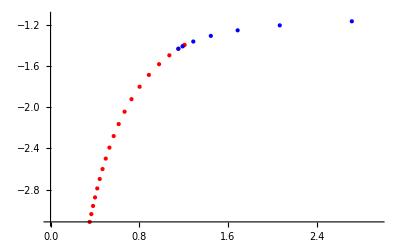

```mathematica
ListPlot[{datam,datab},PlotStyle->{Red,Blue}]
```

```mathematica
datam=Table[{1/(FreeEnergyM[1+i/100,2,1/100,100][[-2]][[1]][[-1]]),FreeEnergyM[1+i/100,2,1/100,100][[-1]]},{i,20}]
```

{{1.20002054933507502324447,-1.39745446253591773},{1.20017003133513202004418,-1.39736053864164949},{1.20072166831501512549761,-1.39701070375184688},{1.20166384043068570268967,-1.3964131669531522},{1.20289285918383877738081,-1.39563508620028741},{1.2042805287776257003781,-1.39475876814572821},{1.2057122533197170973117,-1.39385713856129724},{1.20709369456024357209051,-1.39298960989945297},{1.20834744469494134528418,-1.3922044133337758},{1.20940926656540751784631,-1.39154121645070639},{1.21022544342591128610314,-1.3910330206016272},{1.21075100230229078826695,-1.39070747959175312},{1.21094847828445594398542,-1.39058784908568635},{1.21078700565539150207667,-1.39069369927407969},{1.2102416117493393859632,-1.39104147060741584},{1.20929264121885263994665,-1.39164491848868094},{1.20792526710748767622821,-1.39251547633876617},{1.20612906144558311738511,-1.39366255620992131},{1.20389760778155526714596,-1.39509380059058536},{1.20122814410395108392082,-1.39681529442306332}}

```mathematica
datab=Table[{1/(FreeEnergyB[9/10+i/100,2,1/100,100][[-2]][[1]][[-1]]),FreeEnergyB[9/10+i/100,2,1/100,100][[-1]]},{i,9}]
```

{{1.15391370948809959580947,-1.42792132711028792},{1.15533852101491833032792,-1.42696672712930604},{1.15782535988914618835894,-1.42529525158167962},{1.16147549671874597622826,-1.42283939790969351},{1.16640243176560402641019,-1.41952999271012736},{1.17272445981601832702783,-1.41530340552068076},{1.18053863125135233493975,-1.41012132866071717},{1.18983138573534567789209,-1.40403088183507236},{1.20010653223937937550935,-1.39739950490521153}}

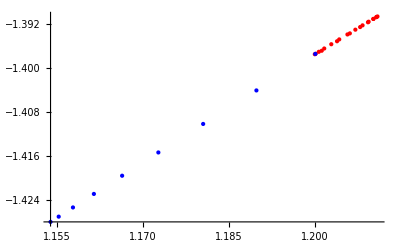

```mathematica
ListPlot[{datam,datab},PlotStyle->{Red,Blue}]
```

```mathematica
F[2]={1.2,-1.397};
```

```mathematica
datam=Table[{1/(FreeEnergyM[1+i/100,3,1/100,100][[-2]][[1]][[-1]]),FreeEnergyM[1+i/100,3,1/100,100][[-1]]},{i,20}]
```

{{1.73715888630774561640892,-3.09849814350948675},{1.7369739735245131375105,-3.09860536935949643},{1.73734246666073095791712,-3.09839950561955944},{1.73840198685457229962678,-3.09780301960970509},{1.74011551331479710861551,-3.09683854203803356},{1.74233681161365950432273,-3.09559088717124682},{1.74488826296499582193516,-3.09416201755237136},{1.7476007130285525276957,-3.09264805004444527},{1.75032391950016387408918,-3.09113331782506617},{1.75292658248225867716811,-3.08969053408158859},{1.75529414825769673558997,-3.0883823093976908},{1.7573266349805594311848,-3.08726269492731917},{1.75893689180885286820983,-3.08637848785850583},{1.76004926205309334253809,-3.08577029719808643},{1.76059854957223957900624,-3.08547341432227696},{1.76052919871887115822864,-3.08551853113054167},{1.75979462066248820769451,-3.08593233902074125},{1.75835661797110755687942,-3.08673803287574792},{1.75618487333684730970076,-3.08795573856349341},{1.75325647835189829742265,-3.08960287727546212}}

```mathematica
datab=Table[{1/(FreeEnergyB[9/10+i/100,3,1/100,100][[-2]][[1]][[-1]]),FreeEnergyB[9/10+i/100,3,1/100,100][[-1]]},{i,9}]
```

{{1.61227947598609357069056,-3.17479176061010623},{1.62135221295248489118354,-3.1689246748968003},{1.6322308244423396301818,-3.16194320750122633},{1.64505156602117013238569,-3.1538011941125007},{1.65993974373246700359435,-3.14447339962218921},{1.67697321594793796748062,-3.13397895380022982},{1.69609134610042865158027,-3.12243415797992171},{1.71684162159619813715037,-3.11019081280907731},{1.73748764334930100602602,-3.09831153955474991}}

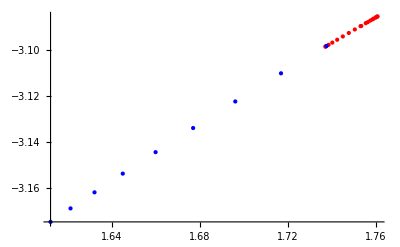

```mathematica
ListPlot[{datam,datab},PlotStyle->{Red,Blue}]
```

```mathematica
F[3]={1.737,-3.099};
```

```mathematica
datam=Table[{1/(FreeEnergyM[1+i/100,4,1/100,100][[-2]][[1]][[-1]]),FreeEnergyM[1+i/100,4,1/100,100][[-1]]},{i,20}]
```

{{2.71765028916480196336788,-5.69418338222960479},{2.71646441741113921541911,-5.6945889051197142},{2.71608189789065777117013,-5.69472286499956096},{2.71706254851818174915054,-5.69439485826946412},{2.71960062100811530025414,-5.69354045584349452},{2.72355529731671627833801,-5.69221065519977317},{2.72862305478694721147556,-5.69051198243630809},{2.73446726916144765617402,-5.68856127444872363},{2.74076836016013281873704,-5.68646803396235016},{2.74723580156071649399388,-5.68433018995876139},{2.75360815901519224159528,-5.68223420582247315},{2.75965046152574493637792,-5.68025626282539881},{2.76515153765187204400962,-5.67846355563520919},{2.76992188800419719174855,-5.67691545960933811},{2.77379210386095658385565,-5.6756645337670291},{2.77661171651087835521747,-5.67475737493748044},{2.77824835456776266077016,-5.67423534659505567},{2.77858710593887616012866,-5.67413520394821447},{2.77753000288328018827541,-5.67448963259862942},{2.77499556719272700989244,-5.67532771476408386}}

```mathematica
datab=Table[{1/(FreeEnergyB[9/10+15/200+i/800,4,1/100,100][[-2]][[1]][[-1]]),FreeEnergyB[9/10+15/200+i/800,4,1/100,100][[-1]]},{i,19}]
```

{{2.65517628875857742579757,-5.7159543141840324},{2.66127007021022363421396,-5.71378260023792156},{2.66734873551910282445671,-5.71162672186893441},{2.67340055025835408353043,-5.70949070287957118},{2.67941195569547489941112,-5.70737912934232638},{2.68536721920148319391549,-5.70529725816786531},{2.69124799437170089279205,-5.70325115454989547},{2.69703275980702514037705,-5.70124786845903071},{2.70269609166424089209439,-5.69929566475959107},{2.7082077034254158776609,-5.69740432913141473},{2.71353115133760957024615,-5.69558558315058086},{2.71862204530697125879361,-5.69385366190582947},{2.72342550235667149745394,-5.69222614173747},{2.72787239072433824791516,-5.69072516924511155},{2.73187354292806941805927,-5.6893793672204847},{2.73531033843573376053881,-5.68822695590135153},{2.73801827446944622619122,-5.68732123030208322},{2.73975568999340072999866,-5.68674104646893487},{2.74013947876448146125258,-5.68661250907989631}}

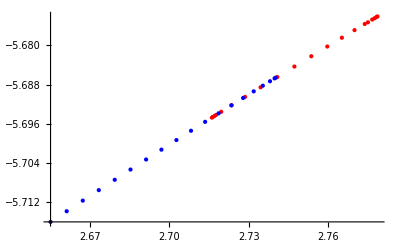

```mathematica
ListPlot[{datam,datab},PlotStyle->{Red,Blue}]
```

```mathematica
datam=Table[{1/(FreeEnergyM[1+i/200,4,1/100,100][[-2]][[1]][[-1]]),FreeEnergyM[1+i/200,4,1/100,100][[-1]]},{i,20}]
```

{{2.71826868985089829460455,-5.6939726948235955},{2.71765028916480196336788,-5.69418338222960479},{2.71700420639212160397969,-5.69440397899524518},{2.71646441741113921541911,-5.6945889051197142},{2.71613024359493534644451,-5.69470431153867065},{2.71608189789065777117013,-5.69472286499956096},{2.71638033551631608430542,-5.69462385973897137},{2.71706254851818174915054,-5.69439485826946412},{2.71813972308054791217009,-5.69403232590457068},{2.71960062100811530025414,-5.69354045584349452},{2.72141803769545821409516,-5.69292892859585387},{2.72355529731671627833801,-5.69221065519977317},{2.72597117603499900181342,-5.69140006114369412},{2.72862305478694721147556,-5.69051198243630809},{2.73146871605504343949595,-5.68956103260139281},{2.73446726916144765617402,-5.68856127444872363},{2.73757956902426890203147,-5.68752607079625867},{2.74076836016013281873704,-5.68646803396235016},{2.74399828079780890955324,-5.68539902691982259},{2.74723580156071649399388,-5.68433018995876139}}

```mathematica
datab=Table[{1/(FreeEnergyB[9/10+15/200+1/80+i/1600,4,1/100,100][[-2]][[1]][[-1]]),FreeEnergyB[9/10+15/200+1/80+i/1600,4,1/100,100][[-1]]},{i,19}]
```

{{2.71089551069414603825377,-5.69648505984976548},{2.71353115133760957024615,-5.69558558315058086},{2.71610881518717384007781,-5.69470776116936369},{2.71862204530697125879361,-5.69385366190582947},{2.72106363507842150550678,-5.6930255927445704},{2.72342550235667149745394,-5.69222614173747},{2.72569853390309230337025,-5.69145822867237315},{2.72787239072433824791516,-5.69072516924511155},{2.72993526116565057337945,-5.69003075667949954},{2.73187354292806941805927,-5.6893793672204847},{2.73367142645684803141237,-5.68877609864381636},{2.73531033843573376053881,-5.68822695590135153},{2.73676818204502718661831,-5.68773910519061339},{2.73801827446944622619122,-5.68732123030208322},{2.7390278229063693586076,-5.68698404499280956},{2.73975568999340072999866,-5.68674104646893487},{2.7401491168895660787705,-5.68660962437897776},{2.74013947876448146125258,-5.68661250907989631},{2.73964339352946933623593,-5.68677747390209159}}

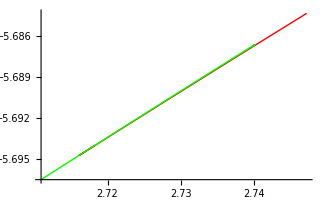

```mathematica
ListLinePlot[{datam,datab},PlotStyle->{Red,Green}]
```

```mathematica
F[4]={2.716,-5.695};
```

```mathematica
datam=Table[{1/(FreeEnergyM[1+i/200,5,1/100,100][[-2]][[1]][[-1]]),FreeEnergyM[1+i/200,5,1/100,100][[-1]]},{i,20}]
```

{{4.99226258920529802868414,-9.374095892259605427},{4.98994969205560131928858,-9.374399369203711991},{4.98720713621601236869197,-9.374759884458451019},{4.98445602679469203106273,-9.375122294727995918},{4.98204078555800876032468,-9.375441306238182637},{4.98027394756327240241863,-9.375675684864210466},{4.97942798489030220039367,-9.375789442948092312},{4.97970738986479429064989,-9.37575563682689347},{4.98122975353353434289705,-9.375558959874675203},{4.98402867149339615394737,-9.375195404961891999},{4.9880724710525967346165,-9.374669780143423052},{4.9932866885745290559018,-9.373992688161755838},{4.99957263767569916761097,-9.373178005147745188},{5.00682007038600529732272,-9.372241139790079262},{5.01491484741038816499487,-9.371197960846772832},{5.02374320336722323630496,-9.370064186193416443},{5.03319393348470848433744,-9.368855058145763572},{5.04315939517492307828884,-9.367585185696432518},{5.05353586813759253536443,-9.366268480397912173},{5.06422358599607528182464,-9.364918143138616852}}

```mathematica
datab=Table[{1/(FreeEnergyB[9/10+15/200+1/80+i/1600,5,1/100,100][[-2]][[1]][[-1]]),FreeEnergyB[9/10+15/200+1/80+i/1600,5,1/100,100][[-1]]},{i,19}]
```

{{4.97160220513305188808758,-9.376813018670929695},{4.97910868542746091288364,-9.37582344092027852},{4.98639965507248575134855,-9.374865350599714432},{4.99345405744211205467951,-9.37394122476262811},{5.00024861482820274753892,-9.37305380694885679},{5.0067574854993281821243,-9.372206150524119159},{5.01295184520709944013321,-9.371401671869763432},{5.01879937094456513534563,-9.370644216325506841},{5.02426359654513742712774,-9.369938140924469404},{5.02930309786277943383674,-9.369288419519569766},{5.03387044801655628638384,-9.368700778171728609},{5.03791085800589522630467,-9.368181872126865541},{5.04136038189492290844286,-9.367739520538303534},{5.04414351768263098822343,-9.367383021655555461},{5.04616998825884417203434,-9.367123578077815736},{5.04733052904598186986467,-9.366974857703121159},{5.0474921148081560810242,-9.366953641635251189},{5.04649708371344869266357,-9.367080002082964356},{5.04420174614145679308689,-9.367372486861467653}}

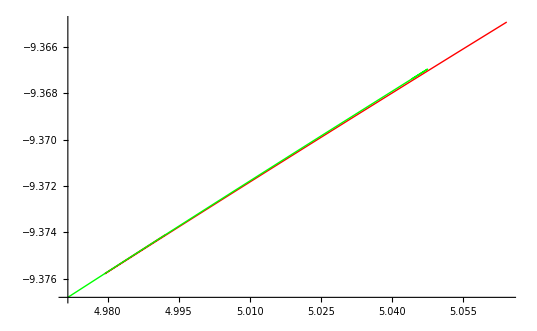

```mathematica
ListLinePlot[{datam,datab},PlotStyle->{Red,Green}]
```

```mathematica
F[5]={4.98,-9.376};
```

```mathematica
datam=Table[{1/(FreeEnergyM[1+i/200,6,1/100,100][[-2]][[1]][[-1]]),FreeEnergyM[1+i/200,6,1/100,100][[-1]]},{i,20}]
```

{{15.8649443943308719555074,-14.28944113442177839},{15.8406752311349850895172,-14.28982391502223943},{15.8097848160291558739951,-14.29031304874655595},{15.776188100231974467462,-14.29084746114178662},{15.7433188367690153450052,-14.29137283509104295},{15.7145052845493964738078,-14.29183568400941593},{15.692838630641461827139,-14.29218566570518655},{15.6808293140677608391094,-14.2923815224596453},{15.6801526309611493965846,-14.29239570612576469},{15.6916337605630759264799,-14.29221504979818167},{15.7154166785645436736974,-14.29183823940547025},{15.7511868769884047371734,-14.29127219406258317},{15.7983608743664977294433,-14.29052884830306639},{15.8562167689845721339989,-14.28962283582603861},{15.9239731476202799068207,-14.28857000714003993},{16.0008321933705170184598,-14.28738654719179041},{16.0860007616068855961153,-14.2860884767718076},{16.1786988576593471293152,-14.28469138433080276},{16.2781613181487712657571,-14.28321029136818944},{16.3836360658881095568687,-14.28165959345391574}}

```mathematica
datab=Table[{1/(FreeEnergyB[9/10+15/200+1/80+i/1600,6,1/100,100][[-2]][[1]][[-1]]),FreeEnergyB[9/10+15/200+1/80+i/1600,6,1/100,100][[-1]]},{i,19}]
```

{{15.6950938610364062659572,-14.29214330271040158},{15.7576778720747053550424,-14.29114122647579589},{15.8182528835242179269071,-14.2901791008631462},{15.8765918690355466863109,-14.28925964495910358},{15.9324463079343090278978,-14.28838585107578419},{15.985543471111771022239,-14.2875610265791584},{16.0355831950285262219326,-14.28678884458201772},{16.0822340102692318459896,-14.28607340586049816},{16.125128449081748266503,-14.28541931523065127},{16.1638573012517073576629,-14.28483177656543543},{16.1979625188957745335892,-14.28431671201873204},{16.226928395800014110322,-14.28388091263743841},{16.2501706021562750477349,-14.28353222889345738},{16.2670227741214264300929,-14.28327980913771547},{16.2767211103616060244502,-14.28313438449821753},{16.2783905664616574497552,-14.28310855496208194},{16.2710491026329566152932,-14.28321684333527105},{16.2537067231840802436852,-14.28347438575191462},{16.2260214363030914151943,-14.28388733255816294}}

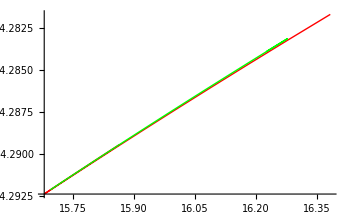

```mathematica
ListLinePlot[{datam,datab},PlotStyle->{Red,Green}]
```

```mathematica
F[6]={15.7,-14.29};
```

```mathematica
databm=Table[{Pi^2i,2/F[i][[1]]},{i,0,6}]
```

{{0,2.60824},{π^2,2.25073},{2 π^2,1.66667},{3 π^2,1.15141},{4 π^2,0.736377},{5 π^2,0.401606},{6 π^2,0.127389}}

```mathematica
datam=Table[{1/(FreeEnergyM[1+i/200,1/2,1/100,100][[-2]][[1]][[-1]]),FreeEnergyM[1+i/200,1/2,1/100,100][[-1]]},{i,20}]
```

{{0.799538681198341142622856,-0.10760724636034634},{0.799588260950797042766183,-0.10760413454978195},{0.799701449155721556298001,-0.10759688747882811},{0.799882484751289150329875,-0.10758522903732701},{0.800128322673054712375732,-0.10756937808462972},{0.800429942004626831657717,-0.10754995254962426},{0.800773857969708800003579,-0.10752786084404428},{0.801144497657021447642274,-0.10750413819490612},{0.801526643136897305808239,-0.10747978187832011},{0.801907006652150734334655,-0.10745565056912034},{0.802274736767583694487634,-0.10743243499998844},{0.802621232661194730589993,-0.10741067543015394},{0.802939704639652109290693,-0.10739079349878647},{0.803224735889468592086928,-0.10737312347888348},{0.803471935168283258069374,-0.10735793800496567},{0.803677686978050647719912,-0.10734546423668461},{0.803838978771684501869394,-0.10733589597641876},{0.803953282305048797740971,-0.10732940264509261},{0.804018471125247895669494,-0.10732613400872426},{0.804032761690096834132208,-0.10732622441359393}}

```mathematica
datab=Table[{1/(FreeEnergyB[9/10+15/200+1/80+i/1600,1/2,1/100,100][[-2]][[1]][[-1]]),FreeEnergyB[9/10+15/200+1/80+i/1600,1/2,1/100,100][[-1]]},{i,19}]
```

{{0.798831436599207669244055,-0.10765534506032581},{0.799061027772765898411973,-0.10763980916589056},{0.799295553873872436381543,-0.10762393606561676},{0.799534841322512716507042,-0.10760773944701279},{0.799778664857297853734019,-0.1075912363827865},{0.800026734524941535348024,-0.1075744491539575},{0.800278678651289822161457,-0.10755740503279839},{0.800534021218437449695235,-0.1075401389925982},{0.800792151293636650061723,-0.10752269510604021},{0.801052280891846940444163,-0.10750512987298015},{0.801313385535776834705646,-0.10748751508221084},{0.801574118074271258336017,-0.10746994462880144},{0.801832679528023046948544,-0.10745254268561667},{0.802086617519308720707846,-0.10743547682557269},{0.802332495220772033778494,-0.10741897922494252},{0.802565310475237295622679,-0.10740338640588954},{0.802777381209416061315626,-0.10738921082718416},{0.80295591405662497681465,-0.10737730147100741},{0.803076523969389906264321,-0.10736927257663662}}

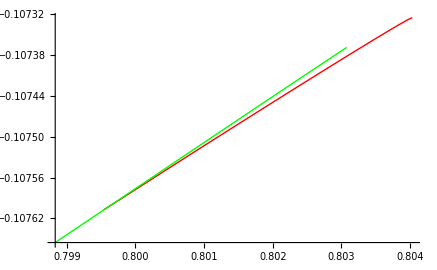

```mathematica
ListLinePlot[{datam,datab},PlotStyle->{Red,Green}]
```

```mathematica
F[1/2]={0.7996,-0.1076};
```

```mathematica
datam=Table[{1/(FreeEnergyM[1+i/200,3/2,1/100,100][[-2]][[1]][[-1]]),FreeEnergyM[1+i/200,3/2,1/100,100][[-1]]},{i,20}]
```

{{1.02075261747464309867648,-0.81604280141428705},{1.02075708912123092377135,-0.816040766940307545},{1.02082939519772139066087,-0.816002622155142378},{1.02098514295953720875858,-0.815920025582026083},{1.0212291178455040509889,-0.815790464129139815},{1.0215579440739539925869,-0.815615819926272297},{1.02196171040122095731282,-0.815401480950345935},{1.02242621500063596824571,-0.81515511731856592},{1.02293554412935843108668,-0.814885285032531434},{1.02347411352224300738397,-0.814600326800102279},{1.02402775948997477672199,-0.814307790131259629},{1.02458405416367281010984,-0.814014264332434069},{1.02513220858561285090412,-0.813725439319729313},{1.0256628353815762303897,-0.81344623904980596},{1.02616770530111392829039,-0.813180957849469013},{1.02663954365588471286184,-0.81293337486172876},{1.027071872738538664294,-0.812706843085379316},{1.02745889296815720933323,-0.812504357493816692},{1.02779539328770243438135,-0.812328607033865752},{1.02807668271515959391681,-0.812182014872033148}}

```mathematica
datab=Table[{1/(FreeEnergyB[9/10+15/200+1/80+i/1600,3/2,1/100,100][[-2]][[1]][[-1]]),FreeEnergyB[9/10+15/200+1/80+i/1600,3/2,1/100,100][[-1]]},{i,19}]
```

{{1.01937856525618888047997,-0.816780581137397473},{1.0198438810735761570904,-0.816530648258131387},{1.02031027092393472525297,-0.816280361572048282},{1.02077702030906942966802,-0.816030108787420862},{1.02124329417246659857533,-0.81578034084986301},{1.02170811177252050116384,-0.815531585002585958},{1.02217031459037129113759,-0.815284461790963004},{1.02262852474298882095598,-0.815039706550084322},{1.02308109019433688145545,-0.814798198122195836},{1.02352601118852089955857,-0.814560997403934692},{1.0239608392623476410875,-0.814329400291386681},{1.02438253496595166882173,-0.814105012176012207},{1.02478726108935559749499,-0.813889856632678512},{1.02517007061409132902889,-0.813686539388777852},{1.02552441323406052887194,-0.813498508146667028},{1.02584130704106186166025,-0.813330488954098964},{1.02610783491371108330793,-0.813189279910127948},{1.02630410886765490867808,-0.813085354818713519},{1.02639621605910852567082,-0.813036596010356632}}

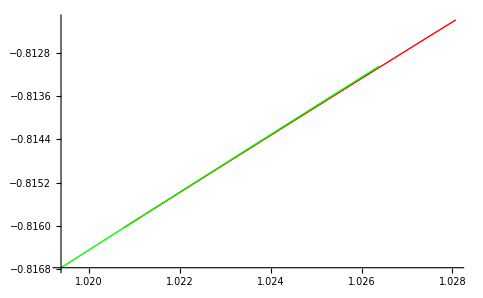

```mathematica
ListLinePlot[{datam,datab},PlotStyle->{Red,Green}]
```

```mathematica
F[3/2]={1.021,-0.816};
```

```mathematica
datam=Table[{1/(FreeEnergyM[1+i/200,5/2,1/100,100][[-2]][[1]][[-1]]),FreeEnergyM[1+i/200,5/2,1/100,100][[-1]]},{i,20}]
```

{{1.43294823772701211728186,-2.14938140395947836},{1.4328488574185362106031,-2.14944544574431949},{1.43281073711900633586979,-2.14947063921427164},{1.43287154189959911521907,-2.14943288484996856},{1.4330526220887998462297,-2.14931855267109869},{1.43336418880068013259699,-2.14912119087138903},{1.43380685320995613764482,-2.14884053953237771},{1.43437301448215593554481,-2.14848162325270335},{1.435049063658483980277,-2.14805331287993775},{1.43581794445483017825914,-2.1475666608334656},{1.43666130274771289060145,-2.1470335074701305},{1.43756088418174835865504,-2.14646557713082451},{1.43849926576714778287238,-2.14587400722487391},{1.43946015396031188306689,-2.14526915875316176},{1.44042844980146156886306,-2.14466057895866686},{1.44139020707769971513231,-2.14405703389592271},{1.44233255044286039531681,-2.14346656782315344},{1.44324358514976513151082,-2.14289656862404794},{1.44411231169237979933411,-2.14235383047234957},{1.44492854990870001624181,-2.14184461041232727}}

```mathematica
datab=Table[{1/(FreeEnergyB[9/10+15/200+1/80+i/1600,5/2,1/100,100][[-2]][[1]][[-1]]),FreeEnergyB[9/10+15/200+1/80+i/1600,5/2,1/100,100][[-1]]},{i,19}]
```

{{1.4303771169635688665063,-2.15102914718151911},{1.43127106872862452692624,-2.1504557183365005},{1.43215635539484225922843,-2.14988861462318929},{1.43303120761750843996697,-2.1493289483145241},{1.43389361275314739839901,-2.14877798123277335},{1.43474126917121463261953,-2.14823715305000908},{1.43557152877263457868393,-2.14770811690555618},{1.43638132367505401979369,-2.14719278488316797},{1.43716707124301918728947,-2.14669338700557356},{1.43792454886692356530245,-2.14621254935492262},{1.43864872544650810277184,-2.14575339913176859},{1.43933352914292817752515,-2.14531970981953418},{1.43997151818077084765723,-2.14491610741263514},{1.44055339831259194678063,-2.1445483729142524},{1.44106728622463766607286,-2.14422390548127514},{1.44149752792486194383432,-2.1439524658599284},{1.4418226855612567410189,-2.14374744578678329},{1.44201187308370529577438,-2.14362818204343106},{1.4420180889893075769569,-2.14362417680303553}}

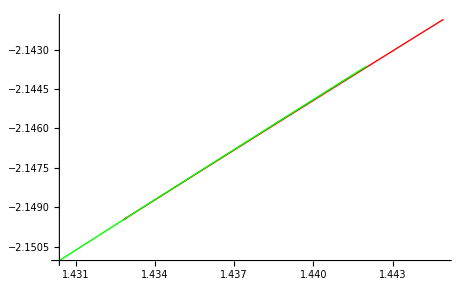

```mathematica
ListLinePlot[{datam,datab},PlotStyle->{Red,Green}]
```

```mathematica
F[5/2]={1.433,-2.149};
```

```mathematica
datam=Table[{1/(FreeEnergyM[1+i/200,7/2,1/100,100][[-2]][[1]][[-1]]),FreeEnergyM[1+i/200,7/2,1/100,100][[-1]]},{i,20}]
```

{{2.14582871161051408397711,-4.27153879072440935},{2.14547980923737825417738,-4.27169971758068994},{2.14515518337276170969193,-4.27184991865498401},{2.14494022499400772135061,-4.27195009195323231},{2.14489425967641108635417,-4.27197291239746842},{2.145060941314071807121,-4.27189830728902259},{2.14546911036533843326541,-4.27171309909542529},{2.14613143285575780590337,-4.27141164427619203},{2.14704487233026791335869,-4.27099560183091843},{2.14819381961117632241821,-4.27047246009712451},{2.14955441161183466396448,-4.26985351064348011},{2.15109841316545628981747,-4.26915202775045013},{2.1527959619895795948659,-4.26838197971734986},{2.15461722454116949573015,-4.26755724992153386},{2.15653327747027072317919,-4.26669122181508736},{2.15851651705993170868184,-4.2657965867510921},{2.16054080753276322245341,-4.26488527645462432},{2.16258149561653529121307,-4.26396846029889474},{2.16461536241080143454986,-4.26305657395159401},{2.16662055010326255496055,-4.26215936140184876}}

```mathematica
datab=Table[{1/(FreeEnergyB[9/10+15/200+1/80+i/1600,7/2,1/100,100][[-2]][[1]][[-1]]),FreeEnergyB[9/10+15/200+1/80+i/1600,7/2,1/100,100][[-1]]},{i,19}]
```

{{2.14082648169719603771574,-4.27384381209014856},{2.14259941656165222846084,-4.27302576807460963},{2.14433993898850028478917,-4.27222414074423863},{2.14604397440914092178203,-4.27144072310017516},{2.14770695121792391557371,-4.2706775245226374},{2.14932371426507876815865,-4.26993680924644127},{2.15088841729940495398479,-4.26922114414275106},{2.1523943875281758841223,-4.26853345897882274},{2.15383395261354543142597,-4.26787712381902306},{2.15519821608597756501892,-4.26725604952659564},{2.15647676038040424939453,-4.26667482120034098},{2.1576572458029846149006,-4.2661388785576514},{2.15872485566248278124164,-4.26565476640807542},{2.15966150682731921287267,-4.26523049146340462},{2.16044469036984908361157,-4.26487604786389272},{2.16104570993046687550905,-4.26460421726002691},{2.16142692789826163828234,-4.26443182250516755},{2.16153755570338560404619,-4.26438165131856577},{2.16131011351578968434486,-4.26448410823954276}}

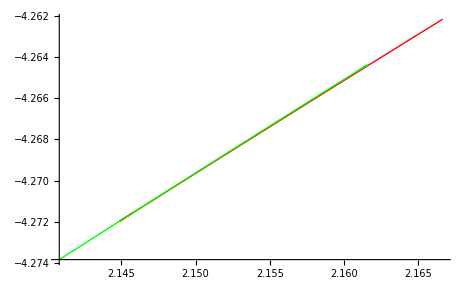

```mathematica
ListLinePlot[{datam,datab},PlotStyle->{Red,Green}]
```

```mathematica
F[7/2]={2.145,-4.272};
```

```mathematica
datam=Table[{1/(FreeEnergyM[1+i/200,9/2,1/100,100][[-2]][[1]][[-1]]),FreeEnergyM[1+i/200,9/2,1/100,100][[-1]]},{i,20}]
```

{{3.57459874468954718108236,-7.388188282775407998},{3.5734596525869098583428,-7.388446826797138481},{3.57217817431978989932787,-7.388738221137847971},{3.57097865243904411705906,-7.389011614714962363},{3.5700364720938608893184,-7.389227141594436568},{3.56950297087993330695603,-7.389350355791479344},{3.56950301934496842393229,-7.389352865901165077},{3.57012342651477394080499,-7.389215042817377082},{3.57140612720996783652884,-7.388927610132793773},{3.57335164384105358317684,-7.388490856701030445},{3.57592944627703882521406,-7.387912245617109934},{3.57908941161515369903405,-7.387203755502965244},{3.58277095133650504442716,-7.386379750465960581},{3.58690908113434886107008,-7.38545555246578229},{3.59143801511639104379556,-7.384446586829606273},{3.59629311187087402333551,-7.383367912756934338},{3.60141183350608378784197,-7.3822339872138752},{3.60673415220070136934838,-7.381058561973230555},{3.61220266397003490773214,-7.379854653308685406},{3.61776255675212276382395,-7.378634549865542846}}

```mathematica
datab=Table[{1/(FreeEnergyB[9/10+15/200+1/80+i/1600,9/2,1/100,100][[-2]][[1]][[-1]]),FreeEnergyB[9/10+15/200+1/80+i/1600,9/2,1/100,100][[-1]]},{i,19}]
```

{{3.56295117995117438811596,-7.39083497389178346},{3.56714911746914795465712,-7.389879275657976733},{3.57124010632288395767606,-7.388950293754906477},{3.57521317997809775065444,-7.388050323488863934},{3.57905615760489169223423,-7.387181916005424584},{3.58275544793495077340358,-7.386347921152019375},{3.58629580826115596379785,-7.385551540272056629},{3.5896600448896625756638,-7.384796392136632345},{3.59282863604010251259896,-7.384086596264696583},{3.59577925034271407224979,-7.383426879660084524},{3.59848612229532222718898,-7.38282271577771802},{3.60091922805831028765306,-7.382280508584292307},{3.60304317725233155077797,-7.381807840795525335},{3.60481569410980403772842,-7.381413815294065651},{3.60618550098053517556772,-7.381109532512723879},{3.60708935681136508880875,-7.380908761290486082},{3.60744810614785673733961,-7.38082884026922863},{3.60716304124322588401831,-7.380891531635960067},{3.60612754438115430131025,-7.381120532656271184}}

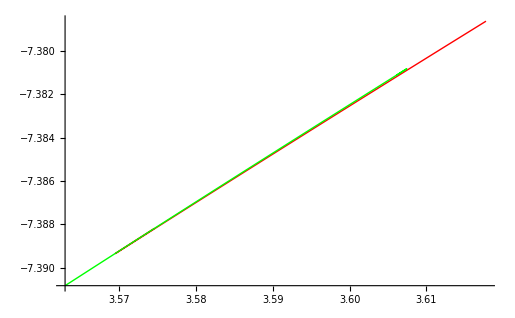

```mathematica
ListLinePlot[{datam,datab},PlotStyle->{Red,Green}]
```

```mathematica
F[9/2]={3.57,-7.389};
```

```mathematica
datam=Table[{1/(FreeEnergyM[1+i/200,11/2,1/100,100][[-2]][[1]][[-1]]),FreeEnergyM[1+i/200,11/2,1/100,100][[-1]]},{i,20}]
```

{{7.7882093646615730978641,-11.66930224589212538},{7.78243927910981230287463,-11.66964720734098972},{7.77531848951127723931966,-11.67007388579107758},{7.76782986947966702174434,-11.67052375763733073},{7.76080924891245138926541,-11.67094671480269654},{7.75504536777288046294767,-11.6712951594366112},{7.75125315253865019981132,-11.67152575462695795},{7.74999607141593211326548,-11.67160430577774849},{7.75162977025179263293123,-11.67150937240203373},{7.7563018914094067112041,-11.67123242218398883},{7.7639945344999669731132,-11.67077530324575534},{7.77457869790894790160008,-11.67014690354475623},{7.78786039309395755842249,-11.6693602661914852},{7.80361254715376860935255,-11.66843055144060191},{7.82159453271128124541738,-11.66737375396932508},{7.84156312509025080483578,-11.66620595364386264},{7.86327817046070449772094,-11.66494290279410692},{7.88650521221753673031318,-11.66359981301686748},{7.9110164583124344952491,-11.66219125598361889},{7.93659089330901340972496,-11.66073112773522994}}

```mathematica
datab=Table[{1/(FreeEnergyB[9/10+15/200+1/80+i/1600,11/2,1/100,100][[-2]][[1]][[-1]]),FreeEnergyB[9/10+15/200+1/80+i/1600,11/2,1/100,100][[-1]]},{i,19}]
```

{{7.74268695766727718853715,-11.67203505905027126},{7.75935581325445501556103,-11.67103095815828968},{7.77550056760393722212386,-11.67006276498698018},{7.79106994915770345998416,-11.66913309646152657},{7.80600755875795930916186,-11.66824484153945616},{7.82025112647866783474574,-11.66740120417720501},{7.83373161266977355516772,-11.66660575574476823},{7.84637210956981990595488,-11.66586249954246591},{7.85808648469975420551622,-11.66517595111421747},{7.86877768613367611967769,-11.6645512393016814},{7.87833560045900751435975,-11.66399423485784321},{7.88663431475614310473479,-11.6635117159633224},{7.89352858522927735303995,-11.66311158326106009},{7.89884927265940545697591,-11.66280314006052035},{7.90239754334319400645907,-11.66259745232306214},{7.90393807619519236706449,-11.66250777948771096},{7.90319383977203743176527,-11.66254993644675007},{7.89985727883536553164865,-11.6627417431044864},{7.89371747396311105949561,-11.66309582080301489}}

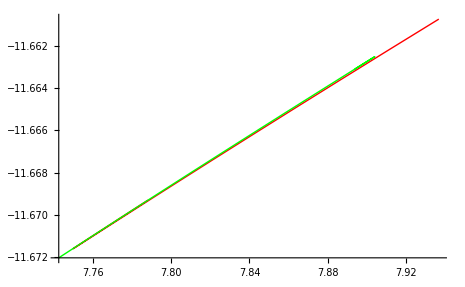

```mathematica
ListLinePlot[{datam,datab},PlotStyle->{Red,Green}]
```

```mathematica
F[11/2]={7.751,-11.67};
```

```mathematica
datam=Table[{FreeEnergyM[1+i/200,651/100,1/100,100][[-2]][[1]][[-1]],FreeEnergyM[1+i/200,651/100,1/100,100][[-1]]},{i,20}]
```

{{0.00223378633313783840200058,-17.31120628177800145},{0.00233099839053316785722399,-17.31162383235674181},{0.00245868004361390930480409,-17.31217243571742136},{0.00260217578263067707807874,-17.31278918131672274},{0.00274797017354355123323938,-17.31341605513455192},{0.00288231301056240688492499,-17.31399407344531548},{0.00299188578813619472758301,-17.31446616135287613},{0.00306542934652972939850132,-17.31478413380576425},{0.00309506241153971234965604,-17.3149143332050008},{0.00307657023575972591278838,-17.31483884348426562},{0.0030088283622955564056564,-17.31455299842164071},{0.00289290483186439189897099,-17.31406151775074141},{0.00273123987014549165933626,-17.31337498147159063},{0.00252704542349541291420709,-17.31250725089024705},{0.00228391526557315039155284,-17.31147379503114424},{0.00200558917785253146600854,-17.31029067922009249},{0.00169581681672001315604963,-17.30897398210771251},{0.00135828206188001876305271,-17.3075394727543177},{0.000996562784194752796339055,-17.30600244011318237},{0.000614110932131762173921096,-17.30437761004264901}}

```mathematica
datab=Table[{FreeEnergyB[9/10+15/200+1/80+i/1600,651/100,1/100,100][[-2]][[1]][[-1]],FreeEnergyB[9/10+15/200+1/80+i/1600,651/100,1/100,100][[-1]]},{i,19}]
```

{{0.00284640759572760367566992,-17.31383718151283631},{0.00261680714702427618259368,-17.31285160387271279},{0.00239733087807245496073293,-17.31190970584944404},{0.00218863599310302779475984,-17.31101427621433042},{0.00199144353410604694077347,-17.31016837436721045},{0.00180654777816970562731788,-17.30937537035962175},{0.00163482752983869734915527,-17.30863899301083375},{0.00147725978771544427032403,-17.30796338819757696},{0.00133493639989110606164095,-17.30735318993881136},{0.00120908448783483873672117,-17.30681360763744596},{0.00110109159771609366145242,-17.30635053362715759},{0.00101253666633376951077928,-17.30597067574354836},{0.00094522774889250475002478,-17.30568171908367843},{0.000901246360964988657532225,-17.30549251659580221},{0.000882994003243900039745341,-17.30541329001948353},{0.00089322110740254019841371,-17.30545575780346004},{0.000934960726871546520265515,-17.30563286050243219},{0.001011032684430258138908,-17.30595666220170763},{0.00112121925890289513723907,-17.306426339450249}}

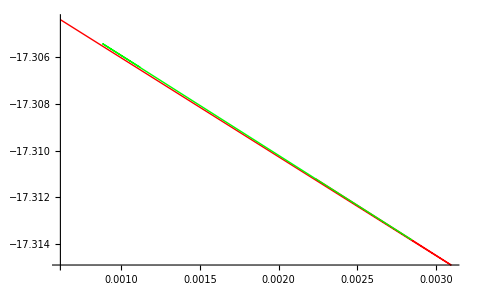

```mathematica
ListLinePlot[{datam,datab},PlotStyle->{Red,Green}]
```

```mathematica
F[13/2]={1/0.002842,-17.31};
```

```mathematica
databm=Table[{Pi^2i/2,2/F[i/2][[1]]},{i,0,13}]
```

{{0,2.60824},{π^2/2,2.50125},{π^2,2.25073},{(3 π^2)/2,1.95886},{2 π^2,1.66667},{(5 π^2)/2,1.39567},{3 π^2,1.15141},{(7 π^2)/2,0.932401},{4 π^2,0.736377},{(9 π^2)/2,0.560224},{5 π^2,0.401606},{(11 π^2)/2,0.258031},{6 π^2,0.127389},{(13 π^2)/2,0.005684}}

```mathematica
Interpolation[databm]
```

InterpolatingFunction[{{0.,64.1524}},<>]

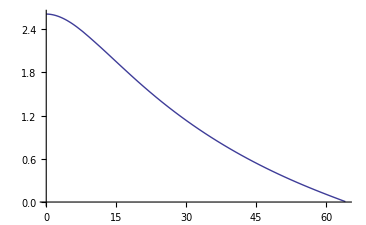

```mathematica
Plot[%119[x],{x,0.,64.15242860708082}]
```